# Weighted Distinct Value Count

## Distinct Value Count

```mathematica
ClearAll[DVC];
DVC::usage = "Counts number of distinct values in TALLY";
DVC[tally_List]:=Length[tally⟦All,2⟧]
```

```mathematica
ClearAll[W];
W[freqs_List]:=With[{fn=freqs/Total[freqs]},(1/Total[Power[fn,2]])]
```

```mathematica
WDVC[tally_List]:=W[tally⟦All,2⟧]
```

Duple case

```mathematica
ClearAll[WW2];
WW2::usage ="gives WDVC for duple {x,y}";
WW2[{x_,y_}]:=With[{f=x/(x+y)},W2[f]]
```

```mathematica
ClearAll[W2];
W2::usage ="gives the WDVC for a duple {f,(1-f)}";
(* conditions *)
W2[0]:=1;
W2[f_ /; f==1/2]:=2;
W2[f_ /; f>1/2]:=W2[1-f];
W2[f_ /; f<1/2]:=g2[f]
```

```mathematica
(* define functional form *)
g1[f_]:=(2-1)/(1/2-0)f+1 (* linear *);
g2[f_]:=1/(f^2+(1-f)^2)
```

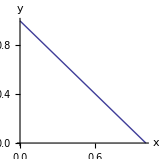

```mathematica
(* Contour plot (line) of normalized values of {x,y} *)
Plot[1-x,{x,0,1},PlotRange->{0,1},AspectRatio->1,AxesLabel->{x,y}]
```

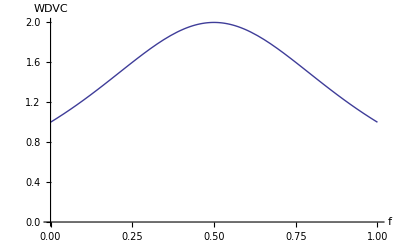

```mathematica
(* Plot of WDVC over this line, i.e., against fraction of mass in x *)
Plot[W2[f],{f,0,1},AxesOrigin->{0,0},AxesLabel->{f,WDVC}]
```

```mathematica
WW2[{0.3,1-0.3}]
```

1.6

Triple case

```mathematica
Module[{eqn,soln,solnZ},
eqn=(x+y+z==1);
soln=Solve[eqn,z];
solnZ=z /. soln⟦1⟧;
Plot3D[solnZ,
{x,0,1},{y,0,1},PlotRange->{0,1},AxesLabel->{x,y,z}] 
]
```

ReplaceAll::reps: {True} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-Graphics3D-

```mathematica
(* contour plot (surface) of all normalized values of {x,y,z} *)

Plot3D[1-x-y,{x,0,1},{y,0,1},PlotRange->{0,1},AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
ClearAll[WW3];
WW3::usage="WDVC of triple {x,y,z}";
WW3[{0,0,z_}]:=1;
WW3[{x_,y_,0}]:=WW2[{x,y}];
WW3[{x_,y_,z_}]:=
Module[{sum,xn,yn,zn,f,g},
sum=x+y+z;
{xn,yn,zn}={x,y,z}/sum;
f=xn/(xn+yn); (* distro between x and y *)
g=(xn+yn)/(xn+yn+zn); (* distro between (x+y) and z *)
W3[f,g]]
```

```mathematica
ClearAll[W3];
W3[f_ /; f==1/2,g_ /; g==2/3]:=3;
```

```mathematica
WW3 /@ { {1,1,1}, {0,1,1}, {1,0,0},{1,0,1}}
```

{3,W3[0,1/2],1,W3[1,1/2]}

## Power

```mathematica
ClearAll[W];
W[freqs_List]:=With[{fn=freqs/Total[freqs]},(1/Total[Power[fn,2]])];
W[freqs_List,power_]:=With[{fn=freqs/Total[freqs]},(1/Total[Power[fn,power]])*(1/2^(power-2))];
```

```mathematica
WDVC[tally_List]:=W[tally⟦All,2⟧]
```

```mathematica
W[{1+delta,1,1,1}]
```

1/(3/(4+delta)^2+(1+delta)^2/(4+delta)^2)

```mathematica
Series[%,{delta,0,3}]
```

4-(3 delta^2)/4+(3 delta^3)/8+O[delta]^4

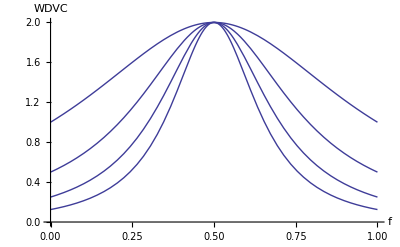

```mathematica
(* Plot of WDVC over this line, i.e., against fraction of mass in x *)
Plot[Table[
W[{f,1-f},m]
,{m,2,5}],
{f,0,1},AxesOrigin->{0,0},AxesLabel->{f,WDVC},PlotRange->Full]
```

```mathematica
?Maximize
```

RowBox[{"Maximize", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["x", "TI"]}], "]"}] maximizes StyleBox["f", "TI"] with respect to StyleBox["x", "TI"].
RowBox[{"Maximize", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] maximizes StyleBox["f", "TI"] with respect to StyleBox["x", "TI"], StyleBox["y", "TI"], …. 
RowBox[{"Maximize", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["f", "TI"], ",", StyleBox["cons", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] maximizes StyleBox["f", "TI"] subject to the constraints StyleBox["cons", "TI"]. 
RowBox[{"Maximize", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["f", "TI"], ",", StyleBox["cons", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["dom", "TI"]}], "]"}] maximizes with variables over the domain StyleBox["dom", "TI"], typically Reals or Integers.

```mathematica
Table[
{m,
Maximize[W[{f,1-f},m],f]⟦1⟧,
2/Maximize[W[{f,1-f},m],f]⟦1⟧,
1/2^(m-2)},
{m,2,8}]  // TableForm
```

2 | 2 | 1 | 1
3 | 2 | 1 | 1/2
4 | 2 | 1 | 1/4
5 | 2 | 1 | 1/8
6 | 2 | 1 | 1/16
7 | 2 | 1 | 1/32
8 | 2 | 1 | 1/64

```mathematica
?PlotRange
```

PlotRange is an option for graphics functions that specifies what range of coordinates to include in a plot.

```mathematica
W[{0,1,1,1},2]
```

3

```mathematica
?Series
```

RowBox[{"Series", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]], ",", StyleBox["n", "TI"]}], "}"}]}], "]"}] generates a power series expansion for StyleBox["f", "TI"] about the point RowBox[{StyleBox["x", "TI"], "=", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}] to order SuperscriptBox[RowBox[{"(", RowBox[{StyleBox["x", "TI"], "-", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], ")"}], StyleBox["n", "TI"]]. 
RowBox[{"Series", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["x", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["0", "TR"]], ",", SubscriptBox[StyleBox["n", "TI"], StyleBox["y", "TI"]]}], "}"}], ",", StyleBox["…", "TR"]}], "]"}] successively finds series expansions with respect to StyleBox["x", "TI"], then StyleBox["y", "TI"], etc.

```mathematica
W[{100,}] // N
```

1.02

```mathematica
DVC[{100,1}]
```

StringJoin::string: String expected at position 1 in Integer <> List.

StringJoin::string: String expected at position 2 in Integer <> List.

Part::partd: Part specification {100, 1} ⟦ All, 2 ⟧ is longer than depth of object.

3